```mathematica
u=0.6;
rh=1.0;
rw=0.5;
dh=0.9;dw=0.4;
alpha=0.4;
beta=300;
p=1;
(*win=807.8125; (*807.8125 for bifurcation*) *)
ws=alpha*(win-beta);
wt= win-ws;

hdot[H_,W_]:=rh*wt*(H)/(H+u*W+p*ws)-dh*H
wdot[H_,W_]:=rw*(wt*(u*W)/(H+u*W+p*ws)+ws)-dw*W
```

```mathematica
eq=Solve[{0==hdot[H,W],0==wdot[H,W]},{W,H}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{W→1.53846 (-300.+win),H→-0.0410256 (-12925.+16. win)},{W→0.0416667 (2400.+7. win-1. √(2.304×10^7-81600. win+241. win^2)),H→0.},{W→0.0416667 (2400.+7. win+√(2.304×10^7-81600. win+241. win^2)),H→0.}}

```mathematica
eq[[1]]
eq[[2]]
eq[[3]]
```

{W→1.53846 (-300.+win),H→-0.0410256 (-12925.+16. win)}

{W→0.0416667 (2400.+7. win-1. √(2.304×10^7-81600. win+241. win^2)),H→0.}

{W→0.0416667 (2400.+7. win+√(2.304×10^7-81600. win+241. win^2)),H→0.}

{807.813,0}

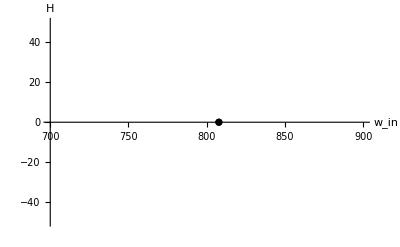

```mathematica
p1=Plot[Evaluate[H/.eq[[1]]],{win,700,807.8125},PlotRange->{{700,900},{-50,50}},AxesLabel->{w_in, H}];
p2=Plot[Evaluate[H/.eq[[1]]],{win,807.8125,900},PlotRange->{{700,900},{-50,50}},AxesLabel->{w_in, H},PlotStyle->{Dashed, Red}];
p3=Plot[Evaluate[H/.eq[[2]]],{win,700,807.8125},PlotRange->{{700,900},{-50,50}},AxesLabel->{w_in, H},PlotStyle->{Dashed, Red}];
p4=Plot[Evaluate[H/.eq[[2]]],{win,807.8125,900},PlotRange->{{700,900},{-50,50}},AxesLabel->{w_in, H}];
point={807.8125,0}
points=ListPlot[{point},PlotStyle->Black,PlotRange->{{700,900},{-50,50}},AxesLabel->{w_in, H}]
```

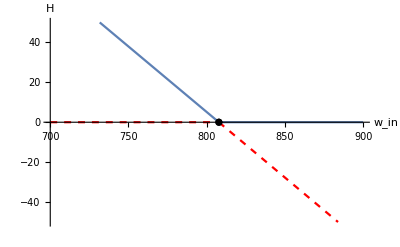

```mathematica
Show[p1,p2,p3,p4,points]
```

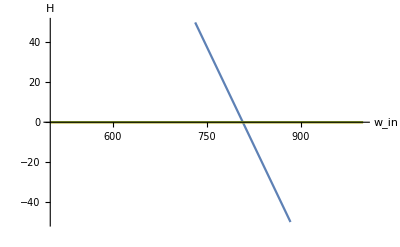

```mathematica
Plot[Evaluate[H/.eq],{win,500,1000},PlotRange->{-50,50},AxesLabel->{w_in, H}]
```